```mathematica
5/Sin[6.28 Degree]
```

45.7091

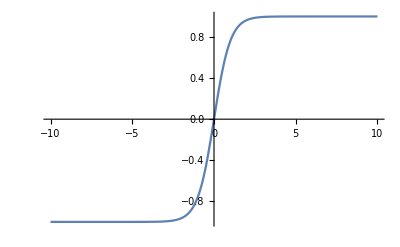

```mathematica
Plot[Tanh[x], {x, -10, 10}]
```

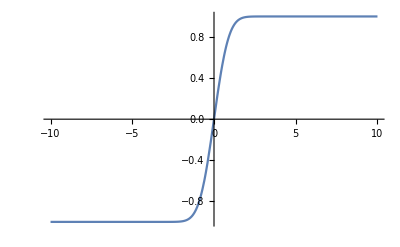

```mathematica
Plot[Erf[x], {x, -10, 10}]
```

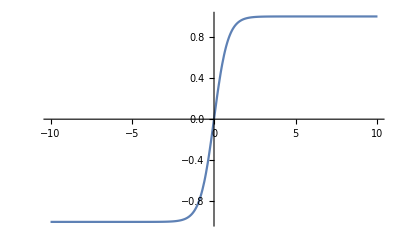

```mathematica
Plot[Tanh[Sqrt[Sqrt[2]]*x], {x, -10, 10}]
```

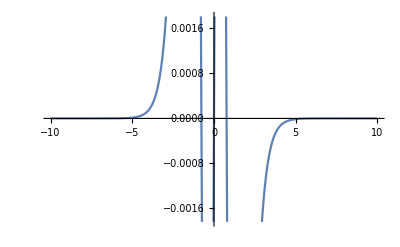

```mathematica
f[x_] = Tanh[Sqrt[Sqrt[2]]*x];
g[x_] = Erf[x];
Plot[f[x] - g[x], {x, -10, 10}]
```

```mathematica
f[1] - g[1]
```

-Erf[1]+Tanh[2^(1/4)]

```mathematica
N[-Erf[1]+Tanh[2^(1/4)]]
```

-0.012368

```mathematica
N[Erf[0.8] - g[0.8]]
```

0.

```mathematica
FindRoot[(x- Sin[x Degree])/Sin[x Degree] == 0.01, {x, 12}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→-0.0441739}

```mathematica
FindRoot[(x- Sin[x Degree])/Sin[x Degree] == 0.01, {x, 10}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→-0.00569991}

```mathematica
0.24* Pi/180
```

0.00418879

```mathematica
0.24 * 180/Pi
```

13.751

```mathematica
4.49 * 180/Pi
```

257.258

```mathematica
FindRoot[Abs[(x- Tan[x ])/Tan[x ]]== 0.01, {x, 3}]
```

{x→0.173032}

```mathematica
x/.{x->0.17303198713330592}
```

0.173032

```mathematica
x/.{x->0.17303198713330592}
```

0.173032

```mathematica
Out[31]*180/Pi
```

{(180 (x→0.173032))/π}

```mathematica
Out[31]
```

{x→0.173032}

```mathematica
x/.Out[31]
```

0.173032

```mathematica
Out[36] * 180/Pi
```

9.914

```mathematica
FindRoot[Abs[(Tan[x] - Sin[x])/Sin[x]] == 0.01, {x, 1}]
```

{x→0.140836}

```mathematica
x/. Out[40]
```

0.140836

```mathematica
Out[42] * 180/Pi
```

8.0693

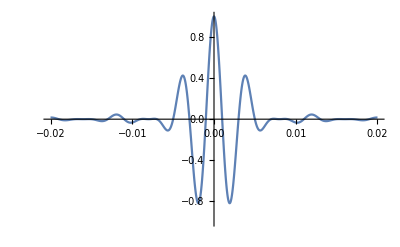

```mathematica
Plot[(Sinc[125 *Pi * y])^2* Cos[500*Pi*y], {y, -0.02, 0.02},PlotRange-> {-1, 1}]
```

```mathematica
Show[%46,ImageSize->Large]
```

```mathematica
Show[%44,ImageSize->Large]
```

```mathematica
5/Sin[8.06 Degree]
```

35.6608